```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (Form Factors)

generic model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC} initialized

classes model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA} initialized

in total: 1 Particles insertion

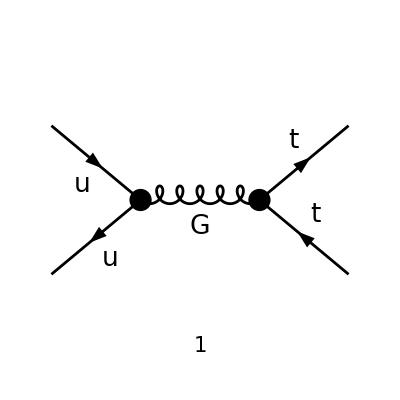

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]},GenericModel->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC"];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 1 Particles amplitude

-ⅈ gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 (MT (φ(-k2)).(γ·p1).(φ(k1)) ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (((ξ_(V(Gen5))-1) (2 π^2 C00eff gs yDM^2+2 π^2 gs p1^2 yDM^2 (C1+C11+C12)-deltaCTL+deltaCTR))/(((p1+p2)^2)^2)+(π^2 gs yDM^2 (C1+2 C11))/(p1+p2)^2)+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (((ξ_(V(Gen5))-1) (-2 π^2 C00eff gs yDM^2-2 π^2 gs p2^2 yDM^2 (C1+C11+C12)+deltaCTL-deltaCTR))/(((p1+p2)^2)^2)+(π^2 gs yDM^2 (C1+2 C12))/(p1+p2)^2))-MT (φ(-k2)).(γ·p2).(φ(k1)) ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (((ξ_(V(Gen5))-1) (-2 π^2 C00eff gs yDM^2-2 π^2 gs p1^2 yDM^2 (C1+C11+C12)+deltaCTL-deltaCTR))/(((p1+p2)^2)^2)+(π^2 gs yDM^2 (C1+2 C12))/(p1+p2)^2)+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (((ξ_(V(Gen5))-1) (2 π^2 C00eff gs yDM^2+2 π^2 gs p2^2 yDM^2 (C1+C11+C12)-deltaCTL+deltaCTR))/(((p1+p2)^2)^2)+(π^2 gs yDM^2 (C1+2 C11))/(p1+p2)^2))+1/(p1+p2)^2(φ(-k2)).γ^Lor2.(φ(k1)) ((φ(p1,MT)).γ^Lor2.(γ̄)^6.(φ(-p2,MT)) (2 π^2 C00eff gs yDM^2+π^2 gs yDM^2 (p1^2 (C1+2 C12)+p2^2 (C1+2 C12)+2 (C12-C11) (p1·p2))+deltaCTR+gs)+(deltaCTL+gs) (φ(p1,MT)).γ^Lor2.(γ̄)^7.(φ(-p2,MT))))

```mathematica
(* Fix Gauge and replace C00eff by the PV loop integrals *)
ampC =ampB/.{LorentzIndex[a_,D]->LorentzIndex[μ,D],GaugeXi[V[Index[Generic,5]]]->1,C00eff->C00-MT^2 (C1+C11+C12)+(s/2)*(C11-C12)}
```

-ⅈ gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 (1/(p1+p2)^2(φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) (2 π^2 gs yDM^2 (C00+MT^2 (-(C1+C11+C12))+1/2 s (C11-C12))+π^2 gs yDM^2 (p1^2 (C1+2 C12)+p2^2 (C1+2 C12)+2 (C12-C11) (p1·p2))+deltaCTR+gs)+(deltaCTL+gs) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))-MT (φ(-k2)).(γ·p2).(φ(k1)) ((π^2 gs yDM^2 (C1+2 C11) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)))/(p1+p2)^2+(π^2 gs yDM^2 (C1+2 C12) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2)+MT (φ(-k2)).(γ·p1).(φ(k1)) ((π^2 gs yDM^2 (C1+2 C11) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2+(π^2 gs yDM^2 (C1+2 C12) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)))/(p1+p2)^2))

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = FullSimplify[Collect[Simplify[ampC],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]];
```

```mathematica
ampEsimp2=FullSimplify[DotSimplify[DiracSimplify[ampE,DiracSubstitute67->True]]]
```

-1/(2 (p1+p2)^2)ⅈ gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 gs yDM^2 (MT (C11-C12) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1)))+C00 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+MT (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))+(2 π^2 C00 gs yDM^2-deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))

```mathematica
sps=Cases2[ampEsimp2,Spinor]
moms=Cases2[ampEsimp2,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^5,γ^μ,γ·p1,γ·p2}

```mathematica
(* phi(k1).p1slash.phi(-k2) + phi(k1).p2slash.phi(-k2) = phi(k1).(p1slash+p2slash).phi(-k2) = phi(k1).(k1slash+k2slash).phi(-k2) = 0 *)
ampEsimp3=Collect[ampEsimp2,{sps[[3]].moms[[1]].sps[[4]]},Simplify]/.{sps[[2]].moms[[3]].sps[[1]]+sps[[2]].moms[[4]].sps[[1]]->0}
```

-1/(2 (p1+p2)^2)ⅈ gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((2 π^2 C00 gs yDM^2-deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+2 π^2 C00 gs yDM^2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+2 π^2 gs MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))+(deltaCTL+deltaCTR) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))

```mathematica
ampEsimp4=FullSimplify[DiracSimplify[DiracSimplify[ampEsimp3,DiracSubstitute5->True]/.(DiracGamma[7]->1-DiracGamma[6])]]
```

-1/(p1+p2)^2 ⅈ gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((2 π^2 C00 gs yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+deltaCTL (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+π^2 gs MT yDM^2 (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
ampF=Collect[ampEsimp4,{sps[[2]].moms[[2]].sps[[1]],sps[[3]].moms[[2]].DiracGamma[6].sps[[4]],sps[[3]].moms[[2]].sps[[4]],sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]]},FullSimplify]
```

(φ(-k2)).γ^μ.(φ(k1)) (-(ⅈ deltaCTL gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(p1+p2)^2-(ⅈ gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 π^2 C00 gs yDM^2-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2)+-(ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)))/(p1+p2)^2+(ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)))/(p1+p2)^2

### Coefficients for each term

```mathematica
factor=FeynAmpDenominator[PropagatorDenominator[Momentum[p1+p2,D],0]]SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]];
CVV = Coefficient[ ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]]]
CVR=Coefficient[ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]]]
CP1=Coefficient[ampF,factor sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]]]
CP2=Coefficient[ampF,factor sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]]]
Coeffs={CVV,CVR,CP1,CP2};
```

-ⅈ deltaCTL gs

-ⅈ gs (2 π^2 C00 gs yDM^2-deltaCTL+deltaCTR)

-ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12)

ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12)